# Simulating Data of form {th1, th2, w1, w2, a1, a2}

This worksheet simulates the SHO and coupled SHO to generate th1, th2 etc but then also uses this ‘perfect’ solution to EL to find out w1, w2 etc and save them off to a data file. This way the errors associated with a discrete differential are avoided.

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
SetDirectory["Documents/Imperial/Year_4/Masters_Project/Code/Goliath/resources"];
```

## SHO oscillator

```mathematica
L[th1_, w1_]:= w1^2 - th1^2;
```

Generate the Euler Equations

```mathematica
sol=EulerEquations[L[th1[t],  D[th1[t],t]], th1[t], t]
```

-2 (th1[t]+th1''[t])==0

```mathematica
sol1=NDSolve[{sol, th1[0]==1, th1[1]==1}, th1[t], {t,0,10.0}]
```

{{th1[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

```mathematica
deltat = 0.1;
```

```mathematica
times = Range[0,10, deltat];
```

```mathematica
expth1 = Flatten[(th1[t]/.sol1)/.t->times];
```

```mathematica
expw1 = Flatten[D[(th1[t]/.sol1), t]/.t->times];
expa1 = Flatten[D[D[(th1[t]/.sol1), t], t]/.t->times];
```

```mathematica
results=Transpose[{expth1, expw1, expa1}];
```

```mathematica
Export["sho_0.1_sim.csv", results, "CSV"];
```

## Coupled SHO

```mathematica
L1[th1_, th2_,  w1_, w2_]:= w1^2 + w2^2 - 2 th1^2 -  th2^2 + 2 th1 th2;
```

Generate the Euler Equations

```mathematica
sol2=EulerEquations[L1[th1[t], th2[t],  D[th1[t],t], D[th2[t],t] ], {th1[t], th2[t]}, t]
```

EulerEquations(L1(th1(t),th2(t),th1'(t),th2'(t)),{th1(t),th2(t)},t)

```mathematica
sol3=NDSolve[{sol2, th1[0]==1, th1[1]==1, th2[0]== 2, th2[1]== 1}, {th1[t], th2[t]}, {t,0,10.0}]
```

{{th1(t)→InterpolatingFunction[{{0., 10.}}, <>](t),th2(t)→InterpolatingFunction[{{0., 10.}}, <>](t)}}

```mathematica
deltat1 = 0.01
```

0.01

```mathematica
times1= Range[0,10, deltat1];
```

```mathematica
expth11 = Flatten[(th1[t]/.sol3)/.t->times1];
```

```mathematica
expth12 = Flatten[(th2[t]/.sol3)/.t->times1];
```

```mathematica
expw11 = Flatten[D[(th1[t]/.sol3), t]/.t->times1];
expa11 = Flatten[D[D[(th1[t]/.sol3), t], t]/.t->times1];
```

```mathematica
expw12 = Flatten[D[(th2[t]/.sol3), t]/.t->times1];
expa12 = Flatten[D[D[(th2[t]/.sol3), t], t]/.t->times1];
```

```mathematica
results1=Transpose[{expth11, expth12, expw11, expw12, expa11, expa12}];
```

```mathematica
Export["sho_coupled_0.01_sim.csv", results1, "CSV"];
```

## Pendulum Attached to a mass on a Spring

Mass M moves horizontally while attached to a spring of spring constant k. Hanging from the mass is a pendulum of arm length L and bob mass m

http://physics.ucsd.edu/students/courses/winter2008/physics110b/LECTURES/CH06_LAGRANGE.pdf

Taking m1 = 1,  m2 =1, k=1, l=1

```mathematica
L2[th_, x_, w1_, xprime_] :=  0.5*(1 + 1)*xprime^2 + 0.5*1*(1^2)*w1^2 + 1*1*Cos[th]*xprime*w1 - 0.5*1*x^2 + 1*9.81*1*Cos[th]
```

Generate the Euler Equations

```mathematica
sol4 = EulerEquations[L2[th1[t], x[t], D[th1[t],t], D[x[t],t]], {th1[t], x[t]}, t]
```

{-1. th1''(t)-cos(th1(t)) x''(t)-9.81 sin(th1(t))==0,-th1''(t) cos(th1(t))+(th1'(t))^2 sin(th1(t))-2. x''(t)-1. x(t)==0}

```mathematica
sol5 = NDSolve[{sol4, th1[0] == 2, th1[1] == 2, x[0] == 1, x[1]== 2}, {th1[t], x[t]}, {t,0,10.0}]
```

{{th1(t)→InterpolatingFunction[{{0., 10.}}, <>](t),x(t)→InterpolatingFunction[{{0., 10.}}, <>](t)}}

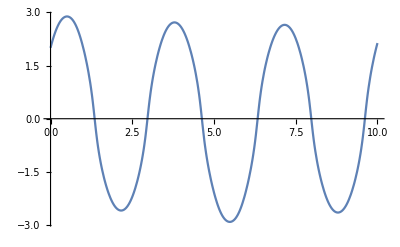

```mathematica
Plot[Evaluate[th1[t]/.sol5], {t, 0,10.0}, PlotRange->All]
```

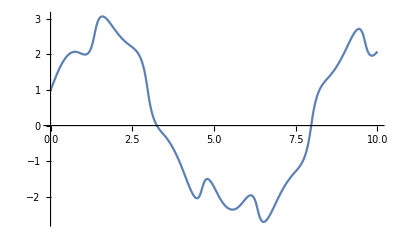

```mathematica
Plot[Evaluate[x[t]/.sol5], {t,0,10.0}, PlotRange->All]
```

```mathematica
delt = 0.1
```

0.1

```mathematica
time = Range[0, 10, delt];
```

```mathematica
datth = Flatten[(th1[t]/.sol5)/.t-> time];
```

```mathematica
datx = Flatten[(x[t]/.sol5)/.t->time];
```

```mathematica
result = Transpose[{datth, datx}]
```

(2. | 1.
2.32251 | 1.22703
2.57249 | 1.45435
2.74748 | 1.65604
2.84968 | 1.82012
2.8845 | 1.94376
2.85423 | 2.02638
2.7552 | 2.06675
2.58067 | 2.06595
2.32789 | 2.03496
2. | 2.
1.5957 | 2.00106
1.09153 | 2.09345
0.414321 | 2.36151
-0.424833 | 2.78266
-1.06776 | 3.01461
-1.53 | 3.0611
-1.88645 | 3.00652
-2.16379 | 2.90056
-2.36993 | 2.77479
-2.50732 | 2.64875
-2.57825 | 2.53254
-2.58461 | 2.43025
-2.52604 | 2.3429
-2.39983 | 2.26852
-2.20311 | 2.19925
-1.93378 | 2.11753
-1.58607 | 1.99368
-1.13838 | 1.78141
-0.527085 | 1.40379
0.29305 | 0.825784
0.986175 | 0.367
1.48951 | 0.0974365
1.88257 | -0.0688142
2.19483 | -0.187063
2.43291 | -0.294163
2.59718 | -0.413676
2.69007 | -0.556783
2.7162 | -0.726053
2.67845 | -0.920553
2.57593 | -1.13801
2.40581 | -1.37275
2.16639 | -1.61136
1.85612 | -1.82947
1.46567 | -1.99004
0.961226 | -2.03595
0.253805 | -1.87466
-0.585567 | -1.58659
-1.21682 | -1.49971
-1.69546 | -1.5708
-2.08303 | -1.72143
-2.39689 | -1.90009
-2.63626 | -2.06913
-2.79856 | -2.20489
-2.88756 | -2.29829
-2.90952 | -2.34834
-2.86633 | -2.35512
-2.75357 | -2.31777
-2.5645 | -2.2385
-2.29751 | -2.13079
-1.95639 | -2.0237
-1.53811 | -1.95963
-1.01398 | -1.99744
-0.301946 | -2.22569
0.533429 | -2.56991
1.14883 | -2.70034
1.59872 | -2.65911
1.94973 | -2.52568
2.22454 | -2.34729
2.42925 | -2.1547
2.56569 | -1.96692
2.63617 | -1.7936
2.64265 | -1.63867
2.58442 | -1.50353
2.45803 | -1.3871
2.26014 | -1.2824
1.98922 | -1.17227
1.64132 | -1.02715
1.19811 | -0.801952
0.602529 | -0.423578
-0.207333 | 0.160792
-0.918957 | 0.652681
-1.42881 | 0.944315
-1.82132 | 1.12321
-2.13036 | 1.24645
-2.36523 | 1.35071
-2.5277 | 1.45929
-2.62011 | 1.58394
-2.64627 | 1.72819
-2.60848 | 1.89166
-2.50593 | 2.07196
-2.33618 | 2.26286
-2.09734 | 2.45045
-1.78647 | 2.61023
-1.39142 | 2.70441
-0.872675 | 2.6726
-0.135989 | 2.42123
0.684079 | 2.08928
1.28943 | 1.96619
1.7551 | 1.98637
2.13381 | 2.0765)

```mathematica
Export["spring-pend_0.1.csv", result, "CSV"];
```